449 Lithium Project 

Group 11: Megan Tabbutt, Ruojun Wang & Huaxia Zhou

Energy units are Hartrees unless otherwise noted

“little z” the variational parameter is zz in our code so it was easier to distinguish by eye from Z (the atomic number)

```mathematica
Import["/Users/megantabbutt/Desktop/Quantum/Defs/448defs.m"]
```

The goal of this project is to use your knowledge of quantum mechanics to compute many of the low-lying energy levels of the Li atom. Since the Li atom has 3 electrons, you will learn how to construct 3-electron wavefunctions that satisfy the Pauli exclusion principle. You will use both variational methods and a basis set expansion to get your final results. You will learn about Slater determinants and exchange operators. You will compare your calculations to experiment, and you should be able to attain accuracies for most of the properties of Li to better than 1% error, and some to less that 0.1% error. Quantum mechanics really works!

To get started, you will first solve the simpler problem of the 1-electron Li++ ion. This simpler calculation is very similar to that of the He atom, written up by a 449 alumnus (Robert Massé) in the paper “Accurate energies of the He atom with undergraduate quantum mechanics”, Am. J.Phys. 83, 730 (2015), which you will need to read carefully. To the methods there, you will add a variational calculation for the ground state, then use a basis set founded on that variational calculation to both improve the ground state energy a bit, and to get the energies of some of the low-lying excited states.

The addition of the third electron in the neutral Li atom adds some complexity to the problem. For Li+ it is sufficient to use an non-symmetrized basis set; the exchange symmetry of the Hamiltonian gives spatial eigenfunctions that are either symmetric or anti-symmetric on interchange, and these are easily identified. For the 3-electron problem, one cannot be so casual and explicitly anti-symmetrized wavefunctions are necessary. To this end, you will constructSlater determinants that satisfy this requirement, and use your knowledge of commutation relations to simplify the calculation of matrix elements of the Hamiltonian. You will again first perform a variational calculation of the ground state energy, then use a related basis set expansion to get the excited states. You will then use a quantum defect analysis of your results to deduce the ionization energy of Li, to an accuracy better than 0.1%.

You will do the above calculations in small 2 or 3 person teams. To ensure proper progress, there will be intermediate due dates for various parts of the project. Once you complete your calculations, each student will write a short (3-5 journal pages) paper on your work. There will be a prize for the best paper and there is also the potential to submit the paper, suitably revised, for publication in a refereed journal.

## Li^(++) - Single Electron Li

The Hamiltonian for the single-electron Li^(++) atom is just like hydrogen, but with a charge of 3 on the nucleus. In atomic units:

								(Ĥ)^(++)= -1/2∇^2 - Z/r
with Z=3 for the Li nucleus.

## Question 1:

1) Show that the radial eigenfunctions of  (Ĥ)^(++) are (P_(n l))^(++)(r) = N(zz) (P_(n l))^(Z r), where P_nl^(r) are the eigenfunctions of hydrogen. Find the normalization factor N(zz). Find the energies.

ⅈ ℏ d/dt ψ = H ψ		(Ĥ)^(++)= -1/2∇^2 - Z/r	 		

For Li^(++) (single electron) radial Eigenfunctions are N(zz) (P_(n l))^(Z r)?

Find the normalization factor using scaling instead: 

Eψ = H ψ		

Take the Radial part: [-ℏ^2/(2m)d^2/dr^2+ (l(l+1)ℏ^2)/(2m r^2)-(e^2 Z)/r]P_(n l) = E P_(n l)	(Townsend 9.98)

Rescale: r=α s		[-ℏ^2/(2m α^2)d^2/ds^2+ (l(l+1)ℏ^2)/(2 m s^2 α^2)-(e^2 Z)/(α s)]P_(n l) = E P_(n l)

				(m α^2)/ℏ^2[-ℏ^2/(2m α^2)d^2/ds^2+ (l(l+1)ℏ^2)/(2 m s^2 α^2)-(e^2 Z)/(α s)]P_(n l) =(m α^2)/ℏ^2 E P_(n l)
						
				[-1/2 d^2/ds^2+ (l(l+1))/(2 s^2)-(m α^2 e^2 Z)/(ℏ^2 α s)]P_(n l) =(m α^2)/ℏ^2 E P_(n l)	

E_s = (m α^2)/ℏ^2 E			[-1/2 d^2/ds^2+ (l(l+1))/(2 s^2)-(m α^2 e^2 Z)/(ℏ^2 α s)]P_(n l) = E_s P_(n l)

Find α by making potential as form above: (m α^2 e^2 Z)/(ℏ^2 α s) =1/s→(m α^2 e^2 Z)/(ℏ^2 α)=1→α=ℏ^2/(Z m e^2)

a_o=ℏ^2/(m e^2) =The Bohr Radius→  α = a_o/Z→  r = a_o/Z s

```mathematica
(* Find the Normalization Factor: *)

Integrate[N^2*Subscript[P, 3,1][Z s]*Subscript[P, 3,1][Z s], {s, 0, ∞}]
```

ConditionalExpression[N^2/Z,Re[Z]>0]

Z is real and greater than 0 so:

N^2/Z=1       →

N=√Z

This is the same as before, there is just a factor of Z from the scaling, but this is the prof Walker approved easier path for later, 
hind sight is 20/20 so take this one...

Show that this is the solution:

Plug into Schrodinger and see if it solves it:

```mathematica
-1/2 D[D[Sqrt[Z]*Subscript[P, 1,0][Z r], r], r] -Z/r *Sqrt[Z]*Subscript[P, 1,0][Z r]== (-Z^2/(2*n^2))(Sqrt[Z]*Subscript[P, 1,0][Z r]) /. {Z -> 1, n -> 1} //FullSimplify
```

True

```mathematica
-1/2 D[D[Sqrt[Z]*Subscript[P, 1,0][Z r], r], r] -Z/r *Sqrt[Z]*Subscript[P, 1,0][Z r]== (-Z^2/(2*n^2))(Sqrt[Z]*Subscript[P, 1,0][Z r]) /. {Z -> 3, n -> 1} //FullSimplify
```

True

It Solves the Schrodinger.

Find the Energies:

From above we know that the energies in atomic units are: -Z^2/(2 n^2)

```mathematica
Table[-Z^2/(2*n^2) /.Z -> 3, {n, 1, 5}] //N
```

{-4.5,-1.125,-0.5,-0.28125,-0.18}

Energies:  -4.5,  -1.125,  -0.5,  -0.28125,  -0.18  Hartrees

## Li^+ - 2 Electron Li

The Hamiltonian for the two-electron Li^+ ion is:

(Ĥ)^+= (Ĥ)^(++)(1) +  (Ĥ)^(++)(2) + 1/r_12 = (Ĥ)_o + V_12 = -1/2(∇_1)^2-Z/r - 1/2(∇_2)^2 - Z/r  + 1/r_12

We are going to restrict our considerations to states of total angular momentum L=0, which we assume is made of only of s-type single-electron orbitals (P_(n l=0))^(++)(r) =  (P_n^zz)^(r) = (√zz )(P_(n l=0))^(++)(zz r). The basis states we will denote simply as:  n_1;n_2, whose representation in position space is: r_1;r_2n_1; n_2 ≡(P_(n_1 n_2))^+(r_1, r_2) = P_n_1^zz(r_1)P_n_2^zz(r_2).

### Question 2:

2) Show that the matrix elements of (Ĥ)^+ are:  n_1 n_2(Ĥ)^+n_3 n_4 = n_1(Ĥ)^(++)n_3 δ_(n_(2,)n_4) + n_2(Ĥ)^(++)n_4 δ_(n_(1,)n_3) + n_1 n_2 V_12 n_3;n_4  . Write Mathematica routines to calculate (analytically)  n_1(Ĥ)^(++)n_3  and n_1;n_2 V_12 n_3;n_4 ; check your results against the Massé paper for He.

Show that the matrix elements of  (Ĥ)^+ are:  n_1 n_2(Ĥ)^+n_3 n_4 = n_1(Ĥ)^(++)n_3 δ_(n_(2,)n_4) + n_2(Ĥ)^(++)n_4 δ_(n_(1,)n_3) + n_1 n_2 V_12 n_3;n_4 . 
 
n_1 n_2(Ĥ)^†n_3 n_4 =n_1 n_2(Ĥ)^(++)(1) +  (Ĥ)^(++)(2) + (1/r_12)^n_3 n_4 =n_1 n_2-1/2(∇_1)^2-Z/r1 - 1/2(∇_2)^2 - Z/r2  + (1/r_12)^n_3 n_4  

(Ĥ)^(++)(1)  only acts on particle one  and the same is true for the second particle so you will get:

n_1 n_2-1/2(∇_1)^2-Z/r1 - 1/2(∇_2)^2 - Z/r2  + (1/r_12)^n_3 n_4 
=n_1 n_2-1/2(∇_1)^2-(Z/r1)^n_3 n_4+n_1 n_2 - 1/2(∇_2)^2 - (Z/r2)^n_3 n_4+n_1 n_2 (1/r_12)^n_3 n_4
=n_1-1/2(∇_1)^2-(Z/r1)^n_3n_2n_4+n_2- 1/2(∇_2)^2 - (Z/r2)^n_4n_1n_3+n_1 n_2 (1/r_12)^n_3 n_4
=n_1(Ĥ)^(++)n_3∫M  P_(n_2 l)*P_(n_4 l)ⅆr+n_2(Ĥ)^(++)n_4∫M * P_(n_2 l)*P_(n_2 l)ⅆr+n_1 n_2 V_12 n_3 n_4 

M is a factor that will have Y_(l m) in it and some constant

Because the P_(n l) Radial wave functions are orthogonal the integral is either 0 or 1 as given below: 
n_1 n_2(Ĥ)^+n_3 n_4 = n_1(Ĥ)^(++)n_3 δ_(n_(2,)n_4)  +  n_2(Ĥ)^(++)n_4 δ_(n_(1,)n_3)  +  n_1 n_2 V_12 n_3 n_4

Write Mathematica routines to calculate (analytically)  n_1(Ĥ)^(++)n_3  and  n_1 n_2(Ĥ)^(++)n_3 n_4  ;


**** Code replicated from "He via degenerate perturbation theory” Notebook on class website ****

```mathematica
(* Z = 3, just define and plug in, leave *)

Subscript[P, n_][zz_,r_]:=√zz Subscript[P, n,0][zz r];
```

```mathematica
(* Formulas for e-e repulsion matrix elements unperturbed energies.The integrals can be done analytically but are somewhat tedious and we find it preferable to just do them numerically.It is not unusual to get warnings from the numerical integration routine but we have never found a case where these matter. *)

V[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[Subscript[P, n1][2,r1]Subscript[P, n2][2,r2]Min[1/r2,1/r1]Subscript[P, n3][2,r1]Subscript[P, n4][2,r2],{r2,0,∞},{r1,0,∞},AccuracyGoal->7]
```

```mathematica
(* Convert to hartree *)

E0[{n1_,n2_}]:=-3^2/n1^2*1/2+-3^2/n2^2*1/2
```

```mathematica
(* Generate the list of states.An unsymmetrized basis is used so the singlet and triplet states are generated from the matrix diagonalization. *)

st=DeleteDuplicates[Table[{{1,i},{i,1}},{i,4}]~Flatten~1]
```

{{1,1},{1,2},{2,1},{1,3},{3,1},{1,4},{4,1}}

```mathematica
(* Hamiltonian, H=H^0+V *)

Vmat=Table[V[st⟦i⟧,st⟦j⟧],{i,Length[st]},{j,Length[st]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1.25,-0.17871,-0.17871,0.0879189,0.0879189,-0.0552137,-0.0552137},{-0.17871,0.419753,0.0438957,-0.101053,-0.0224458,0.0574314,0.0142681},{-0.17871,0.0438957,0.419753,-0.0224458,-0.101053,0.0142681,0.0574314},{0.0879189,-0.101053,-0.0224458,0.198975,0.0115356,-0.0576774,-0.007345},{0.0879189,-0.0224458,-0.101053,0.0115356,0.198975,-0.007345,-0.0576774},{-0.0552137,0.0574314,0.0142681,-0.0576774,-0.007345,0.115267,0.00467927},{-0.0552137,0.0142681,0.0574314,-0.007345,-0.0576774,0.00467927,0.115267}}

```mathematica
H=DiagonalMatrix[E0/@st]+Vmat;
H//MatrixForm
```

(-7.75 | -0.17871 | -0.17871 | 0.0879189 | 0.0879189 | -0.0552137 | -0.0552137
-0.17871 | -5.20525 | 0.0438957 | -0.101053 | -0.0224458 | 0.0574314 | 0.0142681
-0.17871 | 0.0438957 | -5.20525 | -0.0224458 | -0.101053 | 0.0142681 | 0.0574314
0.0879189 | -0.101053 | -0.0224458 | -4.80103 | 0.0115356 | -0.0576774 | -0.007345
0.0879189 | -0.0224458 | -0.101053 | 0.0115356 | -4.80103 | -0.007345 | -0.0576774
-0.0552137 | 0.0574314 | 0.0142681 | -0.0576774 | -0.007345 | -4.66598 | 0.00467927
-0.0552137 | 0.0142681 | 0.0574314 | -0.007345 | -0.0576774 | 0.00467927 | -4.66598)

Do it for Arbitrary zz:

```mathematica
ϵϵ[n_]:=With[{Ppsi=Subscript[P, n][zz,r]},Integrate[Ppsi*(-1/2 D[Ppsi, r,r]-zz/r Ppsi),{r,0,∞}]]
VV[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[Subscript[P, n1][zz,r1]Subscript[P, n2][zz,r2]Min[1/r2,1/r1]Subscript[P, n3][zz,r1]Subscript[P, n4][zz,r2],{r2,0,∞},{r1,0,∞},AccuracyGoal->7]
```

```mathematica
VV1[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[Subscript[P, n1][2,r1]Subscript[P, n2][2,r2]Min[1/r2,1/r1]Subscript[P, n3][2,r1]Subscript[P, n4][2,r2],{r2,0,∞},{r1,0,∞},AccuracyGoal->7]
ϵϵ1[zz_,n_]:=With[{Ppsi=Subscript[P, n][zz,r]},Integrate[Ppsi*(-1/2 D[Ppsi, r,r]-2/r Ppsi),{r,0,∞}]]
2*ϵϵ1[2,1]+VV1[{1,1},{1,1}]//N
```

-2.75

This checks out with the Masse paper.

Check your results against the Massé paper for He.

Plug in Z=2 and check:

```mathematica
(* Z = 2, *)

Subscript[P, n_][r_]:=2^(1/2)*Subscript[P, n,0][2r]
```

```mathematica
(* Formulas for e-e repulsion matrix elements unperturbed energies.The integrals can be done analytically but are somewhat tedious and we find it preferable to just do them numerically.It is not unusual to get warnings from the numerical integration routine but we have never found a case where these matter. *)

V[{n1_,n2_},{n3_,n4_}]:=
NIntegrate[Subscript[P, n1][r1]Subscript[P, n3][r1]Min[1/r2,1/r1]Subscript[P, n2][r2]Subscript[P, n4][r2],{r2,0,∞},{r1,0,∞},AccuracyGoal->7];E0[{n1_,n2_}]:=-2/n1^2+-2/n2^2
```

```mathematica
(* Generate the list of states.An unsymmetrized basis is used so the singlet and triplet states are generated from the matrix diagonalization. *)

st=DeleteDuplicates[Table[{{1,i},{i,1}},{i,4}]~Flatten~1]
```

{{1,1},{1,2},{2,1},{1,3},{3,1},{1,4},{4,1}}

```mathematica
(* Hamiltonian, H=H^0+V *)

Vmat=Table[V[st⟦i⟧,st⟦j⟧],{i,Length[st]},{j,Length[st]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
H=DiagonalMatrix[E0/@st]+Vmat;
```

```mathematica
(* Calculate eigenvalues for 1s1s,(1s2s)^3 S,(1s2s)^1 S *)
H//MatrixForm
```

(-2.75 | -0.17871 | -0.17871 | 0.0879189 | 0.0879189 | -0.0552137 | -0.0552137
-0.17871 | -2.08025 | 0.0438957 | -0.101053 | -0.0224458 | 0.0574314 | 0.0142681
-0.17871 | 0.0438957 | -2.08025 | -0.0224458 | -0.101053 | 0.0142681 | 0.0574314
0.0879189 | -0.101053 | -0.0224458 | -2.02325 | 0.0115356 | -0.0576774 | -0.007345
0.0879189 | -0.0224458 | -0.101053 | 0.0115356 | -2.02325 | -0.007345 | -0.0576774
-0.0552137 | 0.0574314 | 0.0142681 | -0.0576774 | -0.007345 | -2.00973 | 0.00467927
-0.0552137 | 0.0142681 | 0.0574314 | -0.007345 | -0.0576774 | 0.00467927 | -2.00973)

This Hamiltonian matches the one in the Masse paper (reference 10 in the paper). So it works.

You are now ready to do a simple variational calculation of the ground state energy of Li+.For your variational wavefunction, pick P_n_1^zz(r_1)P_n_2^zz(r_2) keeping zz to be your variational parameter.

## Question 3:

3) Minimize the ground-state (1s)^2) energy with respect to zz, and compare your results to the NIST experimental energy. Make a physical argument why zz<Z.

Guess the form:

```mathematica
Clear[zz]
$Assumptions=Re[zz]>0;

Subscript[P, n_][zz_,r_]:=√zz Subscript[P, n,0][zz r];
(*Z=3*)
ϵc[zz_,n_]:=With[{Ppsi=Subscript[P, n][zz,r]},Integrate[Ppsi*(-1/2 D[Ppsi, r,r]-3/r Ppsi),{r,0,∞}]]
```

```mathematica
Vc[{n1_,n2_},{n3_,n4_}]:=
Integrate[Subscript[P, n1][zz,r1]Subscript[P, n2][zz,r2]Min[1/r2,1/r1]Subscript[P, n3][zz,r1]Subscript[P, n4][zz,r2],{r2,0,∞},{r1,0,∞}]

Vc[{1,1},{1,1}]
```

(5 zz)/8

```mathematica
Solve[D[(2*ϵc[z,1]+(5 z)/8), z]==0,z]//N
```

{{z→2.6875}}

```mathematica
Energy3 = 2*ϵc[zz1,1]+(5 *zz1)/8/.zz1 -> 2.6875
```

-7.22266

Energy=-196.539 eV=-7.22266 Hartree

Ionization energy as listed in NIST for 1 s^2 for Li III = 122.4543581 eV, Li II=75.6400964

eV to Hartree according to NIST =

```mathematica
EnergyNIST = -(122.4543581 + 75.6400964)/27.21138602
```

-7.27984

NIST Energy = -7.27984 Hartree

```mathematica
Percent = (EnergyNIST - Energy3)/EnergyNIST*100
```

0.785467

Percent Difference: 0.785467%

The nucleus has a Positive charge of Z. The electrons around the nucleus will have a negative charge, call it q. When you view the nucleus of the atom from an area outside that which has a q charge worth of electrons in between you and nucleus you will see an effective charge of Z -q. This is the idea of the shielding electrons. The electrons between you and the nucleus are “shielding” some of the positive charge. This can be seen from the ideas of Gauss’s law. So thus the effective charge you will see is Z - q, where Z > 0 and q < 0, thus zz is like an effective charge and so it cant be bigger than Z and in fact with any amount of q it is smaller, which is what we see.

Now make a somewhat more sophisticated calculation. Your variational wavefunction for the 1 s^2 state should be a pretty good representation. So use the set of functions P_n_1^zz(r_1)P_n_2^zz(r_2) as a basis, with zz chosen as the result of your variational calculation. Make a list of the 17 lowest energy states and use those as a basis. Even though all the 17^2 integrals can be done analytically, in the interest of time it is useful to do them numerically.

Make a list of the 17 lowest energy states and use those as a basis.

The lowest 17 energy states are 1s1s,1s2s,2s1s,1s3s,3s1s,1s4s,4s1s,1s5s,5s1s,
1s6s,6s1s,1s7s,7s1s,1s8s,8s1s,1s9s,9s1s.

## Question 4:

4) Use your 17 state basis to construct the Hamiltonian for Li^+, and find the energy eigenvalues. How much better is your 1 s^2 energy?

```mathematica
st4=DeleteDuplicates[Table[{{1,i},{i,1}},{i,9}]~Flatten~1]
```

{{1,1},{1,2},{2,1},{1,3},{3,1},{1,4},{4,1},{1,5},{5,1},{1,6},{6,1},{1,7},{7,1},{1,8},{8,1},{1,9},{9,1}}

```mathematica
Clear[zz]
Subscript[P, n_][zz_,r_]:=√zz Subscript[P, n,0][zz r];

H44[n1_,n3_, zz_]:=NIntegrate[Subscript[P, n1][zz, r](-1/2 D[Subscript[P, n3][zz,r], {r, 2}]-3/r Subscript[P, n3][zz,r]),{r,0,∞}]
V44[{n1_, n2_},{n3_,n4_}, zz_]:=NIntegrate[Subscript[P, n1][zz, r1]Subscript[P, n3][zz, r1]Min[1/r2,1/r1]Subscript[P, n2][zz,r2]Subscript[P, n4][zz,r2],{r2,0,∞},{r1,0,∞}]
```

```mathematica
H441= Table[H44[st4⟦i⟧⟦1⟧,st4⟦j⟧⟦1⟧,2.6875]KroneckerDelta[st4⟦i⟧⟦2⟧,st4⟦j⟧⟦2⟧]+H44[st4⟦i⟧⟦2⟧,st4⟦j⟧⟦2⟧,2.6875]KroneckerDelta[st4⟦i⟧⟦1⟧,st4⟦j⟧⟦1⟧]+V44[{st4⟦i⟧⟦1⟧, st4⟦i⟧⟦2⟧},{st4⟦j⟧⟦1⟧,st4⟦j⟧⟦2⟧}, 2.6875],{i,Length[st4]},{j,Length[st4]}];
H441//MF
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(-7.22 | -0.0642 | -0.0642 | 0.0272 | 0.0272 | -0.0161 | -0.0161 | 0.0111 | 0.0111 | -0.00822 | -0.00822 | 0.00643 | 0.00643 | -0.00521 | -0.00521 | 0.00434 | 0.00434
-0.0642 | -5. | 0.059 | -0.0752 | -0.0302 | 0.0413 | 0.0192 | -0.0276 | -0.0136 | 0.0203 | 0.0103 | -0.0157 | -0.00813 | 0.0127 | 0.00664 | -0.0106 | -0.00556
-0.0642 | 0.059 | -5. | -0.0302 | -0.0752 | 0.0192 | 0.0413 | -0.0136 | -0.0276 | 0.0103 | 0.0203 | -0.00813 | -0.0157 | 0.00664 | 0.0127 | -0.00556 | -0.0106
0.0272 | -0.0752 | -0.0302 | -4.68 | 0.0155 | -0.047 | -0.00987 | 0.0283 | 0.007 | -0.0199 | -0.0053 | 0.0151 | 0.00419 | -0.012 | -0.00342 | 0.00992 | 0.00287
0.0272 | -0.0302 | -0.0752 | 0.0155 | -4.68 | -0.00987 | -0.047 | 0.007 | 0.0283 | -0.0053 | -0.0199 | 0.00419 | 0.0151 | -0.00342 | -0.012 | 0.00287 | 0.00992
-0.0161 | 0.0413 | 0.0192 | -0.047 | -0.00987 | -4.57 | 0.00629 | -0.0311 | -0.00446 | 0.0198 | 0.00338 | -0.0144 | -0.00267 | 0.0112 | 0.00218 | -0.00911 | -0.00183
-0.0161 | 0.0192 | 0.0413 | -0.00987 | -0.047 | 0.00629 | -4.57 | -0.00446 | -0.0311 | 0.00338 | 0.0198 | -0.00267 | -0.0144 | 0.00218 | 0.0112 | -0.00183 | -0.00911
0.0111 | -0.0276 | -0.0136 | 0.0283 | 0.007 | -0.0311 | -0.00446 | -4.53 | 0.00316 | -0.0219 | -0.00239 | 0.0145 | 0.00189 | -0.0108 | -0.00155 | 0.00858 | 0.0013
0.0111 | -0.0136 | -0.0276 | 0.007 | 0.0283 | -0.00446 | -0.0311 | 0.00316 | -4.53 | -0.00239 | -0.0219 | 0.00189 | 0.0145 | -0.00155 | -0.0108 | 0.0013 | 0.00858
-0.00822 | 0.0203 | 0.0103 | -0.0199 | -0.0053 | 0.0198 | 0.00338 | -0.0219 | -0.00239 | -4.5 | 0.00181 | -0.0163 | -0.00143 | 0.011 | 0.00117 | -0.00838 | -0.000981
-0.00822 | 0.0103 | 0.0203 | -0.0053 | -0.0199 | 0.00338 | 0.0198 | -0.00239 | -0.0219 | 0.00181 | -4.5 | -0.00143 | -0.0163 | 0.00117 | 0.011 | -0.000981 | -0.00838
0.00643 | -0.0157 | -0.00813 | 0.0151 | 0.00419 | -0.0144 | -0.00267 | 0.0145 | 0.00189 | -0.0163 | -0.00143 | -4.49 | 0.00114 | -0.0125 | -0.000927 | 0.00864 | 0.000776
0.00643 | -0.00813 | -0.0157 | 0.00419 | 0.0151 | -0.00267 | -0.0144 | 0.00189 | 0.0145 | -0.00143 | -0.0163 | 0.00114 | -4.49 | -0.000927 | -0.0125 | 0.000776 | 0.00864
-0.00521 | 0.0127 | 0.00664 | -0.012 | -0.00342 | 0.0112 | 0.00218 | -0.0108 | -0.00155 | 0.011 | 0.00117 | -0.0125 | -0.000927 | -4.48 | 0.000758 | -0.00992 | -0.000634
-0.00521 | 0.00664 | 0.0127 | -0.00342 | -0.012 | 0.00218 | 0.0112 | -0.00155 | -0.0108 | 0.00117 | 0.011 | -0.000927 | -0.0125 | 0.000758 | -4.48 | -0.000634 | -0.00992
0.00434 | -0.0106 | -0.00556 | 0.00992 | 0.00287 | -0.00911 | -0.00183 | 0.00858 | 0.0013 | -0.00838 | -0.000981 | 0.00864 | 0.000776 | -0.00992 | -0.000634 | -4.47 | 0.000531
0.00434 | -0.00556 | -0.0106 | 0.00287 | 0.00992 | -0.00183 | -0.00911 | 0.0013 | 0.00858 | -0.000981 | -0.00838 | 0.000776 | 0.00864 | -0.000634 | -0.00992 | 0.000531 | -4.47)

```mathematica
(* The energy Eigenvalues: *)

{eval44, evec44} = Eigensystem[H441]; eval44
```

{-7.22701,-5.06543,-4.9809,-4.70306,-4.6788,-4.5876,-4.57727,-4.53655,-4.53127,-4.50961,-4.50661,-4.49371,-4.49188,-4.4835,-4.48203,-4.43792,-4.38792}

Ground state energy of Li+ : -7.22701 Hartrees

```mathematica
Percent = (EnergyNIST - eval44⟦1⟧)/EnergyNIST*100
```

0.725628

Percent Difference: 0.725628%

That is about .08% better than previously, so it is a little bit better, still sub 1%

## Question 5:

5) Looking at your eigenvectors, which ones are singlets and which ones are triplets? Calculate the 1s2s singlet and triplet energies, and compare to experiment. Also compare the singlet-triplet splitting to experiment.

Which ones are singlets and which ones are triplets?

```mathematica
EvecMatrix = Table[evec44⟦i⟧, {i, 1, 17}];
EvecMatrix //MF
```

(0.999 | 0.0273 | 0.0273 | -0.00927 | -0.00927 | 0.00515 | 0.00515 | -0.00344 | -0.00344 | 0.00252 | 0.00252 | -0.00196 | -0.00196 | 0.00158 | 0.00158 | -0.00132 | -0.00132
-1.11×10^-9 | -0.702 | 0.702 | -0.0812 | 0.0812 | 0.0245 | -0.0245 | -0.0133 | 0.0133 | 0.0089 | -0.0089 | -0.00657 | 0.00657 | 0.00516 | -0.00516 | -0.00423 | 0.00423
0.0317 | -0.671 | -0.671 | -0.205 | -0.205 | 0.065 | 0.065 | -0.0377 | -0.0377 | 0.0261 | 0.0261 | -0.0198 | -0.0198 | 0.0158 | 0.0158 | -0.0131 | -0.0131
7.62×10^-8 | 0.0691 | -0.0691 | -0.672 | 0.672 | -0.197 | 0.197 | 0.0522 | -0.0522 | -0.029 | 0.029 | 0.0198 | -0.0198 | -0.015 | 0.015 | 0.0121 | -0.0121
0.0142 | -0.14 | -0.14 | 0.596 | 0.596 | 0.338 | 0.338 | -0.0825 | -0.0825 | 0.0479 | 0.0479 | -0.0337 | -0.0337 | 0.0261 | 0.0261 | -0.0214 | -0.0214
-3.93×10^-9 | -0.0308 | 0.0308 | 0.147 | -0.147 | -0.61 | 0.61 | -0.315 | 0.315 | 0.065 | -0.065 | -0.0371 | 0.0371 | 0.0261 | -0.0261 | -0.0205 | 0.0205
0.00861 | -0.0728 | -0.0728 | 0.186 | 0.186 | -0.491 | -0.491 | -0.457 | -0.457 | 0.0758 | 0.0758 | -0.0475 | -0.0475 | 0.0349 | 0.0349 | -0.0282 | -0.0282
-1.67×10^-9 | 0.0189 | -0.0189 | -0.0744 | 0.0744 | 0.197 | -0.197 | -0.517 | 0.517 | -0.427 | 0.427 | 0.0601 | -0.0601 | -0.0389 | 0.0389 | 0.0295 | -0.0295
0.00592 | -0.0472 | -0.0472 | 0.104 | 0.104 | -0.201 | -0.201 | 0.368 | 0.368 | 0.554 | 0.554 | -0.0461 | -0.0461 | 0.0403 | 0.0403 | -0.033 | -0.033
0 | -0.0132 | 0.0132 | 0.0479 | -0.0479 | -0.109 | 0.109 | 0.218 | -0.218 | -0.402 | 0.402 | -0.523 | 0.523 | 0.0366 | -0.0366 | -0.0373 | 0.0373
-0.00437 | 0.0337 | 0.0337 | -0.0693 | -0.0693 | 0.12 | 0.12 | -0.189 | -0.189 | 0.239 | 0.239 | 0.621 | 0.621 | 0.00287 | 0.00287 | 0.0316 | 0.0316
4.56×10^-9 | 0.00986 | -0.00986 | -0.0343 | 0.0343 | 0.0722 | -0.0722 | -0.13 | 0.13 | 0.212 | -0.212 | -0.277 | 0.277 | -0.596 | 0.596 | -0.00135 | 0.00135
-0.00339 | 0.0257 | 0.0257 | -0.0509 | -0.0509 | 0.0834 | 0.0834 | -0.123 | -0.123 | 0.158 | 0.158 | -0.115 | -0.115 | -0.658 | -0.658 | -0.0643 | -0.0643
-5.6×10^-10 | 0.00819 | -0.00819 | -0.0278 | 0.0278 | 0.0562 | -0.0562 | -0.0954 | 0.0954 | 0.146 | -0.146 | -0.199 | 0.199 | 0.173 | -0.173 | 0.629 | -0.629
0.00319 | -0.024 | -0.024 | 0.0465 | 0.0465 | -0.0738 | -0.0738 | 0.105 | 0.105 | -0.134 | -0.134 | 0.138 | 0.138 | -0.0246 | -0.0246 | -0.666 | -0.666
-5.59×10^-10 | -0.0334 | 0.0334 | 0.101 | -0.101 | -0.173 | 0.173 | 0.239 | -0.239 | -0.291 | 0.291 | 0.323 | -0.323 | -0.334 | 0.334 | 0.318 | -0.318
0.0204 | -0.139 | -0.139 | 0.219 | 0.219 | -0.271 | -0.271 | 0.293 | 0.293 | -0.292 | -0.292 | 0.276 | 0.276 | -0.251 | -0.251 | 0.221 | 0.221)

We can determine what is a singlet and what is a triplet state by looking at the coefficient in the eigenvectors. The columns are the basis states (1s1s, 1s2s, 2s1s, etc) that we constructed above. Then each row is an eigenvector of the Hamiltonian. If the coefficient of the Evec for the 1s1s state is large such as the first Evec then we know that that wavefunction for the ground state is almost entirely 1s1s, which is good and how we constructed it to be since we parameterized with zz to fit that one best. Next we look to see if there is a large contribution in the 1s2s and 2s1s states and if those are equal and opposite coefficients. Then we know that that is a triplet state and anti-symmetric wavefunction. if there is not this condition then it is a singlet state.

Evec | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
Sing/Trip? | Sing | trip | Sing | Trip | Sing | Trip | Sing | Trip | Sing | trip | Sing | Trip | Sing | Trip | Sing | Trip | Sing

Calculate the 1s2s singlet and triplet energies, and compare to experiment.

For this we will use the 2nd and third eigenvector which are both mostly in the 1s2s state.

```mathematica
MineMine1s2sTrip = eval44⟦1⟧ - eval44⟦2⟧ 
MineMine1s2sSing =eval44⟦1⟧ - eval44⟦3⟧
```

-2.16158

-2.24612

```mathematica
(* Convert Rydbergs to hartrees  by 1/2 factor *)
EnergyNIST1s2sTrip = -4.3379499/2
EnergyNIST1s2sSing = -4.477735/2
```

-2.16897

-2.23887

```mathematica
PercentTrip = (EnergyNIST1s2sTrip - MineMine1s2sTrip)/EnergyNIST1s2sTrip*100
PercentSing = Abs[(EnergyNIST1s2sSing - MineMine1s2sSing)]/Abs[EnergyNIST1s2sSing]*100
```

0.340913

0.323763

Percent Difference between our Calculated 1s2s Singlet and NIST: 0.323763%
Percent Difference between our Calculated 1s2s Triplet and NIST: 0.340913%

Also compare the singlet-triplet splitting to experiment.

```mathematica
SingTripSplittingMineMine = Abs[MineMine1s2sTrip - MineMine1s2sSing] 
SingTripSplittingNIST = Abs[EnergyNIST1s2sTrip - EnergyNIST1s2sSing]
```

0.0845355

0.0698926

```mathematica
PercentSplitting = Abs[(SingTripSplittingNIST - SingTripSplittingMineMine)]/Abs[SingTripSplittingNIST]*100
```

20.9506

Percent Difference between our Calculated 1s2s Splitting between Triplet and Singlet and NIST: 20.9506%

## Li - 3 Electrons

The Hamiltonian for the three-electronLi atom is

(Ĥ)^+= (Ĥ)^(++)(1) +  (Ĥ)^(++)(2) +  (Ĥ)^(++)(3)+1/r_12 +1/r_13+1/r_23  = (Ĥ)_o + V_12+ V_13 + V_23

The Hamiltonian commutes with the exchange operators P12,P13,P23. But these operators do not commute with each other, so the eigenvectors can be chosen to be eigenvectors of one of the exchange operators but not (necessarily) all. But the Pauli exclusion principle says that the valid eigenvectors must be eigenvectors of all three exchange operators, with eigenvalue -1 for each?How does that work?!?

As withLi+, the fact that the Hamiltonian contains no spin operators does not mean that the spin has no effect on the energy. Again, the requirement of anti-symmetry of the wave function on interchange of any pair of atoms will strongly restrict the possible allowed states and energies of the Hamiltonian. The Hamiltonian will have many mathematically allowed states that violate thePauli exclusion principle.

Putting aside these extremely important issues for the moment, we define some notation.The three electrons have spin-1/2, so the eigenfunctions of (Ĥ)^(++) will have both spatial and spin parts. We will denote a single electron spin-orbital by r⃗a = ϕ[a]χ[a]. Here ϕ[a] is a generic orbital(spatial) function, usually equal to one of the (P_n^(++)(r)Y_(l m))/r, and χ[a] is either |u⟩ or |d⟩, depending on the electron’s spin-projection along the z-axis. A 3-electron spin-orbital will be denoted (r⃗)_1(r⃗)_2(r⃗)_3a b c = ϕ[a, b, c]χ[a, b, c] where φ[a,b,c]=φ[a]φ[b]φ[c] and χ[a,b,c] might be u u d for example. Electron #1 is always listed first, followed by 2 and 3. 

As a specific example, a 1s 1s 2s basis function would be (r⃗)_1(r⃗)_2(r⃗)_31s d;  1s u, 2su  = ϕ[1, 1, 2]d u u = (P_1^(++)(r1)Y_00)/r1(P_2^(++)(r2)Y_00)/r2(P_3^(++)(r3)Y_00)/r3 d⊗u⊗u

The exchange operators are defined by, for example: P_12 a b c=b a c 

Products of exchange operators produce cyclic permutations of the state. For example, a left-rotation is produced by the operator

ℒ̂ a b c = P13 P23a b c= P13 a c b = b c a

while a right-rotation, equivalent to two left-rotations, is

ℜ̂ a b c = P23 P13a b c= P23 c b a = c a b  = (ℒ̂)^2 a b c

## Question 6:

6) Calculate  P_23, P_13. Give your answer in terms of ℒ and ℛ. Show that ℒ , H  = ℛ, H = 0. Show that ℒ^3= 1 and ℒ^† = ℛ. Are ℒ^†and ℛ unitary, Hermitian, or what?

CalculateP23, P13. Give your answer in terms of ℒ and ℛ.

Using the definitions listed above for R and L:

P23, P13 |a b c⟩ = P23 P13 |a b c⟩  - P13 P23 |a b c⟩  = (ℜ̂ - ℒ̂) |a b c⟩

P23, P13 =ℜ̂ -ℒ̂

Show that ℒ , H  = ℛ, H = 0.

Using the definitions listed above for R and L:

ℒ , H    =  P13 P23 , H   = P13 , H  P23 + P13  P23 , H   = 0*P23 + P13 *0   = 0 (Townsend 12.36)

ℛ , H    =  P23 P13 , H   = P23 , H  P13 + P23  P13 , H   = 0*P13 + P23 *0   = 0  (Townsend 12.36)

ℛ , H    = ℒ  , H    = 0

Show that ℒ^3= 1 and ℒ^† = ℛ .

ℒ^3 = ℒ ℒ ℒ = P13 P23 P13 P23 P13 P23

ℒ^3 |a b c⟩ = ℒ ℒ ℒ |a b c⟩ = P13 P23 P13 P23 P13 P23 |a b c⟩ = P13 P23 P13 P23 P13 |a c b⟩ = P13 P23 P13 P23  |b c a⟩  = P13 P23 P13   |b a c⟩   
= P13 P23  |c a b⟩  = P13  |c b a⟩  =   |a b c⟩    Thus ℒ^3= 1 , where 1 is the identity matrix. 

ℒ^† |a b c⟩=(P13(P23))^† |a b c⟩  		( A B )^† = B^† A^†

For arbitrary operator and  state: Mk=m|k⟩k M^† =mk 

For ℒ  Op: 	 a b cℒ d e f =a b ce f d  		
For ℒ^†  Op: 	  a b cℒ^† d e f =d e fℒ a b c =d e fb c a 

For  ℛ Op: 	 a b cℛ d e f =a b cf d e  		
For ℛ^†  Op:  	a b cℛ^† d e f =d e fℛ a b c =d e fc a b  	

But you can notice:	 	ℒ^† =d e fb c a   =dbecfa =af  bd⟨c|e⟩=a b cf d e  =ℛ

Thus ℒ^3= 1 , where 1 is the identity matrix. 
Thus,  ℒ^† = ℛ

Are ℒ^†and ℛ unitary, Hermitian, or what?

An Operator is Unitary if 		A A^† = 1, where 1 is the identity matrix. 

ℒ^†ℒ = ℛ ℒ  =  P23 P13 P13 P23 = P23 P13^2 P23 = P23 1 P23 = P23^2 = 1, Where we have noted that Pij^2= 1 by definition, and 1 is the identity matrix. 
So ℒ^† is Unitary. 

ℛ ℛ^† = ℛ ℒ  =  P23 P13 P13 P23 = P23 P13^2 P23 = P23 1 P23 = P23^2 = 1, Where we have noted that Pij^2= 1 by definition, and 1 is the identity matrix. 
So ℛ is Unitary. 

An operator is Hermitian if: 	A = A^†:
 
ℒ^† =  ℛ ≠ ℒ 			So ℒ  is not Hermitian. 
ℛ =  ℒ^†  ≠ ℛ^†			So ℛ  is not Hermitian.

ℒ^† is Unitary,  ℒ  is not Hermitian. 
 ℛ is Unitary,  ℛ  is not Hermitian.

## Question 7:

7) Prove that if |ψ⟩ is an eigenvector of P12 and P23  with eigenvalue -1, it is also an eigenvector of P13 with eigenvalue -1. One way to do this is to calculate Q = P23 P12 . Show that Q |ψ⟩ = |ψ⟩. Then P13 |ψ⟩ =P13 Q |ψ⟩ = ...

Given: 		Q = P23 P12		P12 |ψ⟩ =  - |ψ⟩		P23 |ψ⟩ =  - |ψ⟩	

Then:
Q |ψ⟩  = P23 P12 |ψ⟩  = P23 ( P12 |ψ⟩  )  = P23 ( - |ψ⟩ )  =  - ( P23 |ψ⟩  ) = - ( - |ψ⟩ ) = |ψ⟩		thus, Q |ψ⟩  = |ψ⟩. 	

Now: 
P13  |ψ⟩  = P13 Q |ψ⟩ = P13 P23 P12 |ψ⟩ 

Side note:		P13 P23a b c  =b c a  
Want: 			X P12a b c  =b c a , 	But: 	X P12a b c  =Xb a c  =b c a   If X = P23

Go back: 	P13  |ψ⟩  = P13 Q |ψ⟩ = P13 P23 P12 |ψ⟩  =  P23 P12 P12 |ψ⟩  = P23 1 |ψ⟩  = P23 |ψ⟩ =  - |ψ⟩ , 	Where 1 is the identity matrix. 

Thus, P13  |ψ⟩  = - |ψ⟩  	so  if |ψ⟩ is an eigenvector of P12 and P23  with eigenvalue -1, it is also an eigenvector of P13 with eigenvalue -1

Q |ψ⟩  = |ψ⟩
If |ψ⟩ is an eigenvector of P12 and P23  with eigenvalue -1, it is also an eigenvector of P13 with eigenvalue -1

## Slater Determinates and the Pauli Exclusion Principle:

See the handout on Slater determinants for an important discussion of what they are and their significance for constructing an appropriate set of 3-electron basis functions.

For Li we have 3 spin-1/2 electrons, so the total orbital angular momentum L⃗ = (L⃗)_1+ (L⃗)_2 + (L⃗)_3 can be 1/2 or 3/2 We know that the lowest state of Li+ has S=0, L=0, so when we add the 3rd electron we expect that the spin quantum number will be S = 1 / 2 (a “doublet”) with L = 0 still. Since S = 1/2 then mS = ±1/2. The only way to make mS = 1/2 is for one of the electrons to be in the |d⟩ state, and other two |u⟩. We make the convention that we list the orbital state of the |d⟩ electron first, then the orbital states of the two |u⟩ electrons. The orbital states of the |u⟩ must always be different, or the Slater determinant would vanish.

## Question 8:

8) Show that a Slater determinant for Li can be written as ‖a d,b u,c u‖=1/(√6)(1+ℒ+ℛ)1-(P̂)_23 a d,b u,c u=1/(√2)𝒜a d,b u,c u. We might call the operator 𝒜 an “antisymmetrizer” as it converts a product state into a Slater determinant.

1/(√6)(1+ℒ+ℛ)1-(P̂)_23 a d,b u,c u
=1/(√6)[(1+ℒ+ℛ) a d,b u,c u-(1+ℒ+ℛ)(P̂)_23 a d,b u,c u]
=1/(√6)[ a d,b u,c u+ℒ a d,b u,c u+ℛ a d,b u,c u-(P̂)_23 a d,b u,c u-ℒ(P̂)_23 a d,b u,c u-ℛ(P̂)_23 a d,b u,c u]
=1/(√6)[ a d,b u,c u+b u,c u,a d+c u,a d,b u-a d,c u,b u-(P̂)_13(P̂)_23 a d,c u,b u-(P̂)_23(P̂)_13 a d,c u,b u]
=1/(√6)[ a d,b u,c u+b u,c u,a d+c u,a d,b u-a d,c u,b u-c u,b u,a d-b u,a d,c u]

‖ad,bu,cu‖=1/(√6)[ a d,b u,c u+b u,c u,a d+c u,a d,b u-a d,c u,b u-c u,b u,a d-b u,a d,c u]→‖a d,b u,c u‖=1/(√6)(1+ℒ+ℛ)1-(P̂)_23 a d,b u,c u=1/(√2)𝒜a d,b u,c u, 
where the operator 𝒜 an “antisymmetrizer” as it converts a product state into a Slater determinant.

## Question 9:

𝒜=(1+ℒ+ℜ)(1-P_23)
𝒜^†=[(1+ℒ+ℜ)(1-P_23)]^†=(1+ℒ+ℜ)^†(1-P_23)^†=(1-P_23)(1+ℒ+ℜ)

ℜ ℒ=ℒ ℜ=1,ℒ^2=ℜ,ℜ^2=ℒ

→𝒜^†𝒜=(1-P_23)(1+ℒ+ℜ)(1+ℒ+ℜ)(1-P_23)=(1-P_23)(1+ℒ+ℜ+ℒ+ℒ^2+ℒ ℜ+ℜ+ℜ ℒ+ℜ^2)(1-P_23)=(1-P_23)3(1+ℒ+ℜ)(1-P_23)=3(1-P_23)𝒜
→ 𝒜^†𝒜=3(1-(P̂)_23)𝒜

‖a d,b u,c u‖=1/(√6)(1+ℒ+ℛ)1-(P̂)_23 a d,b u,c u=1/(√2)𝒜a d,b u,c u

→ ‖a ,b ,c‖Ĥ‖A ,B ,C‖
=(1/(√6)a,b,c𝒜)Ĥ(1/(√6)𝒜A,B,C)
=1/6 a,b,c𝒜(Ĥ)^†𝒜A,B,C
=1/6 a,b,c 𝒜𝒜^†Ĥ A,B,C
=1/6 a,b,c 𝒜^†𝒜 Ĥ A,B,C

## Question 10:

1/6 a d,b u,c u 𝒜^†𝒜 Ĥ A d,B u,C u
=1/2 a d,b u,c u(1-P_23)(1-P_23) (1+ℒ+ℜ)Ĥ A d,B u,C u      (*Given by the Problem 9: (1-P_23)3(1+ℒ+ℜ)(1-P_23)=3(1-P_23)𝒜*)
=1/2[(a d,b u,c u(1-P_23))^2 Ĥ A d,B u,C u +(a d,b u,c u(1-P_23))^2 ℒ Ĥ A d,B u,C u +(a d,b u,c u(1-P_23))^2 ℜ Ĥ A d,B u,C u ]
=1/2[(a d,b u,c u(1-P_23))^2 Ĥ A d,B u,C u +(a d,b u,c u(1-P_23))^2 Ĥ A u,B d,C u +(a d,b u,c u(1-P_23))^2 Ĥ A u,B d,C u ]
=1/2(a d,b u,c u(1-P_23))^2 Ĥ A d,B u,C u 

=1/2[a d,b u,c u(1-P_23) Ĥ A d,B u,C u -a d,b u,c u(1-P_23) Ĥ A d,C u,B u ]
=a ,b ,c Ĥ A ,B ,C -a ,b ,c Ĥ A,C,B 


(1-P_23)^2=(1-P_23)(1-P_23)=1-2 P_23+P_23^2=2-2 P_23=2(1-P_23) 

1/2 a d,b u,c u(1-P_23)^2 Ĥ A d,B u,C u 
=a d,b u,c u (1-P_23) Ĥ A d,B u,C u
=1/2 a d,b u,c u Ĥ A d,B u,C u -a d,b u,c u P_23) Ĥ A d,C u,B u
=a u,b u ,c u Ĥ A u ,B u,C u -a u ,b u ,c u Ĥ A u,C u,B u

## Question 11:

Extend your code for  Li^+ to calculate the Slater determinant matrix elements for the Li Hamiltonian.

```mathematica
Subscript[P, n_,l_,zz_][r_]:=√zz Subscript[P, n,l][zz r]
```

```mathematica
H11a[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=n3,n6  n2,n5 NIntegrate[Subscript[P, n1,0,zz][r] (-1/2 D[Subscript[P, n4,0,zz][r], r,r]-Z/r Subscript[P, n4,0,zz][r]),{r,0,∞}];
H11b[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=n3,n6  n1,n4 NIntegrate[Subscript[P, n2,0,zz][r] (-1/2 D[Subscript[P, n5,0,zz][r], r,r]-Z/r Subscript[P, n5,0,zz][r]),{r,0,∞}];
H11c[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=n1,n4  n2,n5 NIntegrate[Subscript[P, n3,0,zz][r] (-1/2 D[Subscript[P, n6,0,zz][r], r,r]-Z/r Subscript[P, n6,0,zz][r]),{r,0,∞}];
V12[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_]:=n3,n6 NIntegrate[Subscript[P, n1,0,zz][r1]Subscript[P, n2,0,zz][r2]Min[1/r2,1/r1]Subscript[P, n4,0,zz][r1]Subscript[P, n5,0,zz][r2],{r2,0,∞},{r1,0,∞}];
V13[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_]:=n2,n5 NIntegrate[Subscript[P, n1,0,zz][r1]Subscript[P, n3,0,zz][r3]Min[1/r3,1/r1]Subscript[P, n4,0,zz][r1]Subscript[P, n6,0,zz][r3],{r3,0,∞},{r1,0,∞}];
V23[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_]:=n1,n4 NIntegrate[Subscript[P, n2,0,zz][r2]Subscript[P, n3,0,zz][r3]Min[1/r2,1/r3]Subscript[P, n5,0,zz][r2]Subscript[P, n6,0,zz][r3],{r2,0,∞},{r3,0,∞}];
```

```mathematica
H11d[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=H11d[{n1,n2,n3},{n4,n5,n6},zz,Z]=(H11a[{n1,n2,n3},{n4,n5,n6},zz,Z]+H11b[{n1,n2,n3},{n4,n5,n6},zz,Z]+H11c[{n1,n2,n3},{n4,n5,n6},zz,Z]+V12[{n1,n2,n3},{n4,n5,n6},zz]+V13[{n1,n2,n3},{n4,n5,n6},zz]+V23[{n1,n2,n3},{n4,n5,n6},zz])-(H11a[{n1,n2,n3},{n4,n6,n5},zz,Z]+H11b[{n1,n2,n3},{n4,n6,n5},zz,Z]+H11c[{n1,n2,n3},{n4,n6,n5},zz,Z]+V12[{n1,n2,n3},{n4,n6,n5},zz]+V13[{n1,n2,n3},{n4,n6,n5},zz]+V23[{n1,n2,n3},{n4,n6,n5},zz]);
```

```mathematica
st11b=Table[{1,1,i},{i,2,3}]
```

{{1,1,2},{1,1,3}}

```mathematica
SlaterDet=Quiet[Table[H11d[st11b⟦i⟧,st11b⟦j⟧,3,3],{i,Length[st11b]},{j,Length[st11b]}]];SlaterDet//MatrixForm
```

(-7.05658 | -0.26949
-0.26949 | -7.04538)

Slater Determinate Matrix = (-7.05658 | -0.26949
-0.26949 | -7.04538)

## Variational Energy of Li

You are now ready to make a variational calculation of the ground state energy of Li. According to the Pauli exclusion principle, the lowest energy wavefunction will likely be of the “1s 1s 2s” form r_1 r_2 r_31s;1s;2s=P_1^z(r_1)P_1^z(r_2)P_2^z(r_3) with again z being an adjustable parameter.

## Question 12:

12) Using a 1s1s2s wavefunction with variable z, find an upper limit on the ground state energy of the Li atom, and compare to experiment.

```mathematica
Clear[zz]
$Assumptions=Re[zz]>0;

H12a[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=n3,n6  n2,n5 Integrate[Subscript[P, n1,0,zz][r] (-1/2 D[Subscript[P, n4,0,zz][r], r,r]-Z/r Subscript[P, n4,0,zz][r]),{r,0,∞}];
H12b[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=n3,n6  n1,n4 Integrate[Subscript[P, n2,0,zz][r] (-1/2 D[Subscript[P, n5,0,zz][r], r,r]-Z/r Subscript[P, n5,0,zz][r]),{r,0,∞}];
H12c[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=n1,n4  n2,n5 Integrate[Subscript[P, n3,0,zz][r] (-1/2 D[Subscript[P, n6,0,zz][r], r,r]-Z/r Subscript[P, n6,0,zz][r]),{r,0,∞}];
Vb12[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_]:=n3,n6 Integrate[Subscript[P, n1,0,zz][r1]Subscript[P, n2,0,zz][r2]Min[1/r2,1/r1]Subscript[P, n4,0,zz][r1]Subscript[P, n5,0,zz][r2],{r2,0,∞},{r1,0,∞}];
Vb13[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_]:=n2,n5 Integrate[Subscript[P, n1,0,zz][r1]Subscript[P, n3,0,zz][r3]Min[1/r3,1/r1]Subscript[P, n4,0,zz][r1]Subscript[P, n6,0,zz][r3],{r3,0,∞},{r1,0,∞}];
Vb23[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_]:=n1,n4 Integrate[Subscript[P, n2,0,zz][r2]Subscript[P, n3,0,zz][r3]Min[1/r2,1/r3]Subscript[P, n5,0,zz][r2]Subscript[P, n6,0,zz][r3],{r2,0,∞},{r3,0,∞}];
H12d[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=H12d[{n1,n2,n3},{n4,n5,n6},zz,Z]=(H12a[{n1,n2,n3},{n4,n5,n6},zz,Z]+H12b[{n1,n2,n3},{n4,n5,n6},zz,Z]+H12c[{n1,n2,n3},{n4,n5,n6},zz,Z]+Vb12[{n1,n2,n3},{n4,n5,n6},zz]+Vb13[{n1,n2,n3},{n4,n5,n6},zz]+Vb23[{n1,n2,n3},{n4,n5,n6},zz])-(H12a[{n1,n2,n3},{n4,n6,n5},zz,Z]+H12b[{n1,n2,n3},{n4,n6,n5},zz,Z]+H12c[{n1,n2,n3},{n4,n6,n5},zz,Z]+Vb12[{n1,n2,n3},{n4,n6,n5},zz]+Vb13[{n1,n2,n3},{n4,n6,n5},zz]+Vb23[{n1,n2,n3},{n4,n6,n5},zz]);
```

```mathematica
ϵ0Li=H12d[{1,1,2},{1,1,2},zz,3] 
ϵ0Li //N
```

(5965 zz)/5832+9/8 (-6+zz) zz

1.02281 zz+1.125 (-6.+zz) zz

```mathematica
Solve[D[((5965 zz)/5832+9/8 (-6+zz) zz), zz]==0,zz]//N
```

{{zz→2.54542}}

```mathematica
Eval12=(5965 2.54541990550221)/5832+9/8 (-6+2.54541990550221) 2.54541990550221
```

-7.28906

Upper limit on the ground state energy of the Li atom: -7.28906 hartrees

Ionization energy as listed in NIST for 1 s^2 for Li III = 9.000229392 Ry, Li II=5.55944459Ry,Li I=0.3962837429Ry

```mathematica
(* Find the Li I energy by looking at Rydberg energy for Li II limit in NIST table, this is in absulate value of energy *)

Nist12Li = 0.3962837429/2;
Nist12LiLi = 5.55944459 /2 ;
Nist12LiLiLi = 9.000229392 /2;

Nist12 = Nist12Li + Nist12LiLi + Nist12LiLiLi
```

7.47798

```mathematica
Percet12 = (1-Abs[Eval12]/Abs[Nist12])*100
```

2.52637

This is 2.52637% different from the NIST value

## Question 13:

13) Thad got about 2.5% error, so let’s try to improve by adding a 1s1s3s orbital to the mix.  Construct the 2×2 Hamiltonian for this basis, find the energies, and minimize the lowest energy. Your answer should significantly improve.

```mathematica
st13=Table[{1,1,i},{i,2,3}]
```

{{1,1,2},{1,1,3}}

```mathematica
H132x2=Table[H12d[st13⟦i⟧,st13⟦j⟧,zz,3],{i,Length[st13]},{j,Length[st13]}]
H132x2 //N
```

{{(5965 zz)/5832+9/8 (-6+zz) zz,-(2766237696 √6 zz)/75429903125-(92 √6 (-3+zz) zz)/3125},{-(2766237696 √6 zz)/75429903125-(92 √6 (-3+zz) zz)/3125,(26811 zz)/32768+19/18 (-6+zz) zz}}

{{1.02281 zz+1.125 (-6.+zz) zz,-0.08983 zz-0.072113 (-3.+zz) zz},{-0.08983 zz-0.072113 (-3.+zz) zz,0.818207 zz+1.05556 (-6.+zz) zz}}

```mathematica
{evals13[zz_],evecs13[zz_]}=Eigensystem[H132x2];
evals13[3] //N
```

{-7.32053,-6.78143}

```mathematica
evals13[zz];
```

```mathematica
(* Minimize and find value of zz to satisfy *)
Solve[D[(evals13[zz]⟦1⟧), zz]==0,zz]//N
```

{{zz→1.99662-0.507061 ⅈ},{zz→1.99662+0.507061 ⅈ},{zz→2.68878}}

```mathematica
(* Find eval with zz value that was found above with minimization process...*)

Eval13Min = evals13[2.6887769456322563]⟦1⟧ //N
```

-7.41623

New ground state energy of the Li atom with minimization process: -7.41623 hartrees

```mathematica
(* Now find the percent difference like in 12 with the NIST value  *)
Percet13 = (1-Abs[Eval13Min]/Abs[Nist12])*100
```

0.825804

```mathematica
(* Our value from 12 is about 3 times the percent off from ours in 13 *)

Percet12/Percet13
```

3.05928

This is 0.825804% different from the NIST value 

(or about 3 times better, percent wise, than our value from 12, and it IS significantly better!)

## Question 14:

Switch to doing the integrals numerically, and add a few more 1s1sns orbitals, maybe even a few 2s1sns.  How much does the answer improve?

```mathematica
(* zz=2.6887769456322563 - from #13  *)
zz=2.6887769456322563 ;
```

```mathematica
st14a=Table[{1,1,i},{i,2,9}]
```

{{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9}}

```mathematica
st14b=Table[{2,1,i},{i,1,3}]
```

{{2,1,1},{2,1,2},{2,1,3}}

```mathematica
(* Group: This takes 20-30 min to run on mine, so beware of executing H14 Matrix... *)

st14={{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,1,11},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{1,1,16},{2,1,2},{2,1,3}, {3, 1, 2}, {1, 2, 3},{2,1,4}, {4, 1, 2}, {1, 2, 4},{2,1,5}, {5, 1, 2}, {1, 2, 5},{2,1,6}, {6, 1, 2}, {1, 2, 6},{2,1,7}, {7, 1, 2}, {1, 2, 7},{3,1,4}, {4, 1, 3}, {1, 3, 4}}

(* If it is taking too long to run use this basis instead: 
st14={{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,1,11},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{1,1,16},{2,1,2},{2,1,3}, {3, 1, 2}, {1, 2, 3},{2,1,4}, {4, 1, 2}, {1, 2, 4}}
*)
(* Need pairs of combinations like in the He Perturbation Theory notebook... 
st14={{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,1,11},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{1,1,16},{2,1,2},{2,1,3},{2,1,4}, {2,1,5}, {2,1,6}, {2,1,7}, {2,1,8}, {3,1,4}, {3,1,5}, {4,1,5},{5,1,6}}*)
```

{{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,1,11},{1,1,12},{1,1,13},{1,1,14},{1,1,15},{1,1,16},{2,1,2},{2,1,3},{3,1,2},{1,2,3},{2,1,4},{4,1,2},{1,2,4},{2,1,5},{5,1,2},{1,2,5},{2,1,6},{6,1,2},{1,2,6},{2,1,7},{7,1,2},{1,2,7},{3,1,4},{4,1,3},{1,3,4}}

```mathematica
H11d[{n1_,n2_,n3_},{n4_,n5_,n6_},zz_,Z_]:=H11d[{n1,n2,n3},{n4,n5,n6},zz,Z]=(H11a[{n1,n2,n3},{n4,n5,n6},zz,Z]+H11b[{n1,n2,n3},{n4,n5,n6},zz,Z]+H11c[{n1,n2,n3},{n4,n5,n6},zz,Z]+V12[{n1,n2,n3},{n4,n5,n6},zz]+V13[{n1,n2,n3},{n4,n5,n6},zz]+V23[{n1,n2,n3},{n4,n5,n6},zz])-(H11a[{n1,n2,n3},{n4,n6,n5},zz,Z]+H11b[{n1,n2,n3},{n4,n6,n5},zz,Z]+H11c[{n1,n2,n3},{n4,n6,n5},zz,Z]+V12[{n1,n2,n3},{n4,n6,n5},zz]+V13[{n1,n2,n3},{n4,n6,n5},zz]+V23[{n1,n2,n3},{n4,n6,n5},zz]);
```

```mathematica
(* Add the quiet function, becuase I get it, you don't like us mathematica.. *)

H14=Quiet[Table[H11d[st14⟦i⟧,st14⟦j⟧,2.688776938,3],{i,Length[st14]},{j,Length[st14]}]];

H14//MatrixForm
```

(-7.26594 | -0.181188 | 0.0995244 | -0.0664833 | 0.0488127 | -0.0379376 | 0.0306413 | -0.0254484 | 0.0215895 | -0.0186254 | 0.0162881 | -0.0144054 | 0.0128616 | -0.0115766 | 0.0104933 | -0.0880074 | 0.0122147 | 0.0381928 | -0.0259781 | -0.00784587 | -0.0229148 | 0.0150689 | 0.00558406 | 0.0158031 | -0.0102191 | -0.00423537 | -0.011783 | 0.0075476 | 0.00335497 | 0.00923785 | -0.00588288 | 0.00365839 | 0.00350441 | 0.000153973
-0.181188 | -7.19778 | -0.114781 | 0.0690339 | -0.0485813 | 0.0369319 | -0.0294378 | 0.0242401 | -0.020443 | 0.0175613 | -0.0153087 | 0.0135062 | -0.0120357 | 0.0108167 | -0.00979224 | 0.0122147 | -0.0714639 | -0.00567073 | -0.0657931 | 0.00420829 | 0.00350441 | 0.000703877 | -0.00299942 | -0.00245283 | -0.000546594 | 0.00227673 | 0.00184415 | 0.00043258 | -0.0018043 | -0.00145325 | -0.000351049 | -0.00196366 | -0.0182698 | 0.0163061
0.0995244 | -0.114781 | -7.19724 | -0.0762411 | 0.0484261 | -0.0352837 | 0.0274938 | -0.0223288 | 0.0186599 | -0.0159272 | 0.0138195 | -0.0121493 | 0.0107969 | -0.00968229 | 0.00874999 | -0.00784587 | 0.00420829 | 0.00365839 | 0.000549904 | -0.0676479 | -0.00226284 | -0.065385 | 0.00193577 | 0.00158433 | 0.00035144 | -0.00146974 | -0.00119136 | -0.000278378 | 0.00116494 | 0.000938912 | 0.00022603 | 0.0288781 | 0.00121525 | 0.0276629
-0.0664833 | 0.0690339 | -0.0762411 | -7.20213 | -0.053833 | 0.0354786 | -0.0265065 | 0.0210425 | -0.0173398 | 0.014662 | -0.0126373 | 0.0110556 | -0.00978824 | 0.00875216 | -0.00789099 | 0.00558406 | -0.00299942 | -0.00260899 | -0.000390425 | 0.00193577 | 0.00161446 | 0.000321317 | -0.0663139 | -0.00113055 | -0.0651833 | 0.0010484 | 0.0008502 | 0.000198196 | -0.000831034 | -0.00067007 | -0.000160964 | -0.000904999 | -0.000867243 | -0.0000377559
0.0488127 | -0.0485813 | 0.0484261 | -0.053833 | -7.20646 | -0.0399061 | 0.0270122 | -0.0205685 | 0.0165683 | -0.013813 | 0.0117926 | -0.0102466 | 0.00902627 | -0.00803963 | 0.00722653 | -0.00423537 | 0.00227673 | 0.00198103 | 0.000295709 | -0.00146974 | -0.00122616 | -0.000243581 | 0.0010484 | 0.000858716 | 0.00018968 | -0.0657293 | -0.000645804 | -0.0650835 | 0.000631102 | 0.000508992 | 0.00012211 | 0.000687406 | 0.000658756 | 0.0000286498
-0.0379376 | 0.0369319 | -0.0352837 | 0.0354786 | -0.0399061 | -7.20974 | -0.0307183 | 0.0212188 | -0.0164001 | 0.0133665 | -0.0112508 | 0.00968233 | -0.00847061 | 0.00750596 | -0.00672012 | 0.00335497 | -0.0018043 | -0.00157026 | -0.000234033 | 0.00116494 | 0.000972063 | 0.000192879 | -0.000831034 | -0.000680801 | -0.000150232 | 0.000631102 | 0.000512015 | 0.000119086 | -0.0654335 | -0.000403552 | -0.0650299 | -0.00054499 | -0.00052229 | -0.0000227002
0.0306413 | -0.0294378 | 0.0274938 | -0.0265065 | 0.0270122 | -0.0307183 | -7.21219 | -0.0243567 | 0.0170945 | -0.0133724 | 0.0110046 | -0.00933714 | 0.00809013 | -0.00711914 | 0.00634066 | -0.00274277 | 0.00147549 | 0.00128428 | 0.000191216 | -0.000952745 | -0.000795101 | -0.000157644 | 0.00067969 | 0.000556883 | 0.000122807 | -0.000516181 | -0.000418827 | -0.0000973543 | 0.000409192 | 0.000330107 | 0.0000790849 | 0.000445796 | 0.000427235 | 0.0000185609
-0.0254484 | 0.0242401 | -0.0223288 | 0.0210425 | -0.0205685 | 0.0212188 | -0.0243567 | -7.21403 | -0.019777 | 0.0140595 | -0.0111079 | 0.00921525 | -0.00787224 | 0.00686068 | -0.00606789 | 0.00229673 | -0.00123579 | -0.00107574 | -0.000160054 | 0.000798019 | 0.000666035 | 0.000131984 | -0.000569326 | -0.000466498 | -0.000102828 | 0.000432374 | 0.000350853 | 0.0000815206 | -0.000342759 | -0.000276535 | -0.0000662247 | -0.000373443 | -0.000357899 | -0.0000155441
0.0215895 | -0.020443 | 0.0186599 | -0.0173398 | 0.0165683 | -0.0164001 | 0.0170945 | -0.019777 | -7.21544 | -0.0163733 | 0.0117636 | -0.00937155 | 0.00782838 | -0.00672665 | 0.00589199 | -0.00195984 | 0.00105468 | 0.000918139 | 0.000136537 | -0.000681097 | -0.000568487 | -0.000112611 | 0.000485921 | 0.000398181 | 0.00008774 | -0.000369036 | -0.000299475 | -0.0000695618 | 0.000292551 | 0.00023604 | 0.0000565111 | 0.000318756 | 0.00030549 | 0.000013265
-0.0186254 | 0.0175613 | -0.0159272 | 0.014662 | -0.013813 | 0.0133665 | -0.0133724 | 0.0140595 | -0.0163733 | -7.21654 | -0.0137762 | 0.00998573 | -0.00801168 | 0.00673214 | -0.00581413 | 0.00169803 | -0.00091388 | -0.000795609 | -0.000118271 | 0.000590194 | 0.000492637 | 0.0000975569 | -0.000421074 | -0.000345059 | -0.0000760156 | 0.000319791 | 0.000259523 | 0.0000602682 | -0.000253513 | -0.000204552 | -0.0000489619 | -0.00027623 | -0.000264737 | -0.0000114936
0.0162881 | -0.0153087 | 0.0138195 | -0.0126373 | 0.0117926 | -0.0112508 | 0.0110046 | -0.0111079 | 0.0117636 | -0.0137762 | -7.21741 | -0.0117502 | 0.00858156 | -0.00692714 | 0.00585084 | -0.00148977 | 0.000801861 | 0.000698112 | 0.000103748 | -0.000517864 | -0.000432279 | -0.0000855855 | 0.000369475 | 0.000302785 | 0.0000666903 | -0.000280605 | -0.000227729 | -0.0000528759 | 0.00022245 | 0.000179493 | 0.000042957 | 0.00024239 | 0.000232306 | 0.0000100843
-0.0144054 | 0.0135062 | -0.0121493 | 0.0110556 | -0.0102466 | 0.00968233 | -0.00933714 | 0.00921525 | -0.00937155 | 0.00998573 | -0.0117502 | -7.21811 | -0.0101396 | 0.00745347 | -0.00604849 | 0.00132089 | -0.000711005 | -0.000619029 | -0.0000919754 | 0.000459196 | 0.000383318 | 0.0000758789 | -0.000327621 | -0.000268493 | -0.0000591285 | 0.00024882 | 0.000201938 | 0.0000468813 | -0.000197253 | -0.000159165 | -0.0000380872 | -0.000214938 | -0.000205997 | -8.94144×10^-6
0.0128616 | -0.0120357 | 0.0107969 | -0.00978824 | 0.00902627 | -0.00847061 | 0.00809013 | -0.00787224 | 0.00782838 | -0.00801168 | 0.00858156 | -0.0101396 | -7.21868 | -0.00883833 | 0.0065337 | -0.00118168 | 0.000636105 | 0.000553831 | 0.0000822738 | -0.00041083 | -0.000342951 | -0.000067879 | 0.000293116 | 0.00024022 | 0.0000528959 | -0.000222615 | -0.000180674 | -0.0000419402 | 0.000176479 | 0.000142406 | 0.0000340733 | 0.000192305 | 0.000184306 | 7.99931×10^-6
-0.0115766 | 0.0108167 | -0.00968229 | 0.00875216 | -0.00803963 | 0.00750596 | -0.00711914 | 0.00686068 | -0.00672665 | 0.00673214 | -0.00692714 | 0.00745347 | -0.00883833 | -7.21915 | -0.00777212 | 0.00106533 | -0.000573496 | -0.000499329 | -0.0000741667 | 0.000370399 | 0.000309206 | 0.0000611931 | -0.000264271 | -0.000216584 | -0.0000476869 | 0.000200708 | 0.000162898 | 0.0000378105 | -0.000159113 | -0.000128394 | -0.0000307184 | -0.000173384 | -0.000166172 | -7.21183×10^-6
0.0104933 | -0.00979224 | 0.00874999 | -0.00789099 | 0.00722653 | -0.00672012 | 0.00634066 | -0.00606789 | 0.00589199 | -0.00581413 | 0.00585084 | -0.00604849 | 0.0065337 | -0.00777212 | -7.21954 | -0.000966905 | 0.000520527 | 0.000453217 | 0.0000673098 | -0.000336192 | -0.000280654 | -0.0000555377 | 0.000239866 | 0.000196586 | 0.0000432804 | -0.000182174 | -0.000147857 | -0.0000343169 | 0.00014442 | 0.00011654 | 0.0000278802 | 0.000157375 | 0.000150829 | 6.54562×10^-6
-0.0880074 | 0.0122147 | -0.00784587 | 0.00558406 | -0.00423537 | 0.00335497 | -0.00274277 | 0.00229673 | -0.00195984 | 0.00169803 | -0.00148977 | 0.00132089 | -0.00118168 | 0.00106533 | -0.000966905 | -5.20338 | -0.103054 | -0.13323 | 0.0301759 | 0.050692 | 0.0698739 | -0.0191819 | -0.0321601 | -0.0457501 | 0.01359 | 0.0229543 | 0.0332371 | -0.0102828 | -0.0175371 | -0.0256708 | 0.0081337 | -0.0111958 | -0.0111958 | 0.
0.0122147 | -0.0714639 | 0.00420829 | -0.00299942 | 0.00227673 | -0.0018043 | 0.00147549 | -0.00123579 | 0.00105468 | -0.00091388 | 0.000801861 | -0.000711005 | 0.000636105 | -0.000573496 | 0.000520527 | -0.103054 | -5.01662 | 0.0201013 | 0.0590129 | -0.0884383 | -0.0111958 | 0. | 0.0503706 | 0.00746484 | 0. | -0.0344635 | -0.00546579 | 0. | 0.0257676 | 0.00423886 | 0. | 0.00767326 | 0.0470735 | -0.0191819
0.0381928 | -0.00567073 | 0.00365839 | -0.00260899 | 0.00198103 | -0.00157026 | 0.00128428 | -0.00107574 | 0.000918139 | -0.000795609 | 0.000698112 | -0.000619029 | 0.000553831 | -0.000499329 | 0.000453217 | -0.13323 | 0.0201013 | -5.06012 | -0.0155084 | -0.0111958 | -0.0983129 | 0.00987453 | 0.00746484 | 0.0573717 | -0.00700112 | -0.00546579 | -0.0397631 | 0.00529951 | 0.00423886 | 0.0299605 | -0.00419291 | 0.0278916 | 0.00767326 | 0.
-0.0259781 | -0.0657931 | 0.000549904 | -0.000390424 | 0.000295709 | -0.000234033 | 0.000191216 | -0.000160054 | 0.000136537 | -0.000118272 | 0.000103749 | -0.0000919754 | 0.0000822738 | -0.0000741667 | 0.0000673098 | 0.0301759 | 0.0590129 | -0.0155084 | -5.02121 | 0. | 0.00987453 | -0.0871171 | 0. | -0.00700112 | 0.0499068 | 0. | 0.00529951 | -0.0342973 | 0. | -0.00419291 | 0.0257216 | 0. | 0.0191819 | -0.0394003
-0.00784587 | 0.00420829 | -0.0676479 | 0.00193577 | -0.00146974 | 0.00116494 | -0.000952745 | 0.000798019 | -0.000681097 | 0.000590194 | -0.000517864 | 0.000459196 | -0.00041083 | 0.000370399 | -0.000336192 | 0.050692 | -0.0884383 | -0.0111958 | 0. | -4.99163 | 0.00643557 | 0.0590129 | -0.0642429 | -0.00434742 | 0. | 0.0393376 | 0.00320475 | 0. | -0.0280907 | -0.0024952 | 0. | -0.0804091 | -0.00356995 | -0.0301759
-0.0229148 | 0.00350441 | -0.00226284 | 0.00161446 | -0.00122616 | 0.000972063 | -0.000795101 | 0.000666035 | -0.000568487 | 0.000492637 | -0.000432279 | 0.000383318 | -0.000342951 | 0.000309206 | -0.000280654 | 0.0698739 | -0.0111958 | -0.0983129 | 0.00987453 | 0.00643557 | -5.04435 | -0.00629076 | -0.00434742 | -0.0687042 | 0.0044613 | 0.00320475 | 0.042715 | -0.00337744 | -0.0024952 | -0.0307631 | 0.0026724 | -0.00356995 | -0.0502332 | 0.
0.0150689 | 0.000703877 | -0.065385 | 0.000321317 | -0.000243581 | 0.000192879 | -0.000157644 | 0.000131984 | -0.00011261 | 0.000097557 | -0.0000855856 | 0.0000758789 | -0.000067879 | 0.0000611932 | -0.0000555377 | -0.0191819 | 0. | 0.00987453 | -0.0871171 | 0.0590129 | -0.00629076 | -4.99177 | 0. | 0.0044613 | -0.0643568 | 0. | -0.00337744 | 0.0395103 | 0. | 0.0026724 | -0.0282679 | -0.0301759 | 0. | -0.0768392
0.00558406 | -0.00299942 | 0.00193577 | -0.0663139 | 0.0010484 | -0.000831034 | 0.00067969 | -0.000569326 | 0.000485921 | -0.000421074 | 0.000369475 | -0.000327621 | 0.000293116 | -0.000264271 | 0.000239866 | -0.0321601 | 0.0503706 | 0.00746484 | 0. | -0.0642429 | -0.00434742 | 0. | -4.98816 | 0.00295308 | 0.0590129 | -0.0473655 | -0.00218315 | 0. | 0.030358 | 0.00170266 | 0. | 0.00344333 | 0.00252285 | 0.
0.0158031 | -0.00245283 | 0.00158433 | -0.00113055 | 0.000858716 | -0.000680801 | 0.000556883 | -0.000466498 | 0.000398181 | -0.000345059 | 0.000302785 | -0.000268493 | 0.00024022 | -0.000216584 | 0.000196586 | -0.0457501 | 0.00746484 | 0.0573717 | -0.00700112 | -0.00434742 | -0.0687042 | 0.0044613 | 0.00295308 | -5.04401 | -0.00316423 | -0.00218315 | -0.0497611 | 0.00239563 | 0.00170266 | 0.0322536 | -0.00189561 | 0.00252285 | 0.00344333 | 0.
-0.0102191 | -0.000546594 | 0.00035144 | -0.0651833 | 0.00018968 | -0.000150233 | 0.000122807 | -0.000102828 | 0.00008774 | -0.0000760156 | 0.0000666903 | -0.0000591285 | 0.000052896 | -0.0000476869 | 0.0000432804 | 0.01359 | 0. | -0.00700112 | 0.0499068 | 0. | 0.0044613 | -0.0643568 | 0.0590129 | -0.00316423 | -4.98795 | 0. | 0.00239563 | -0.047578 | 0. | -0.00189561 | 0.030551 | 0. | 0. | 0.000920478
-0.00423537 | 0.00227673 | -0.00146974 | 0.0010484 | -0.0657293 | 0.000631102 | -0.000516181 | 0.000432374 | -0.000369036 | 0.000319791 | -0.000280605 | 0.00024882 | -0.000222615 | 0.000200708 | -0.000182174 | 0.0229543 | -0.0344635 | -0.00546579 | 0. | 0.0393376 | 0.00320475 | 0. | -0.0473655 | -0.00218315 | 0. | -4.98886 | 0.00161637 | 0.0590129 | -0.0360229 | -0.00126174 | 0. | -0.00258822 | -0.00190325 | 0.
-0.011783 | 0.00184415 | -0.00119136 | 0.0008502 | -0.000645804 | 0.000512015 | -0.000418827 | 0.000350853 | -0.000299475 | 0.000259523 | -0.000227729 | 0.000201938 | -0.000180674 | 0.000162898 | -0.000147857 | 0.0332371 | -0.00546579 | -0.0397631 | 0.00529951 | 0.00320475 | 0.042715 | -0.00337744 | -0.00218315 | -0.0497611 | 0.00239563 | 0.00161637 | -5.04606 | -0.00181379 | -0.00126174 | -0.0374582 | 0.00143524 | -0.00190325 | -0.00258822 | 0.
0.0075476 | 0.00043258 | -0.000278378 | 0.000198196 | -0.0650835 | 0.000119086 | -0.0000973544 | 0.0000815205 | -0.0000695618 | 0.0000602683 | -0.000052876 | 0.0000468813 | -0.0000419402 | 0.0000378105 | -0.0000343169 | -0.0102828 | 0. | 0.00529951 | -0.0342973 | 0. | -0.00337744 | 0.0395103 | 0. | 0.00239563 | -0.047578 | 0.0590129 | -0.00181379 | -4.98866 | 0. | 0.00143524 | -0.0361964 | 0. | 0. | -0.000684966
0.00335497 | -0.0018043 | 0.00116494 | -0.000831034 | 0.000631102 | -0.0654335 | 0.000409192 | -0.000342759 | 0.000292551 | -0.000253513 | 0.00022245 | -0.000197253 | 0.000176479 | -0.000159113 | 0.00014442 | -0.0175371 | 0.0257676 | 0.00423886 | 0. | -0.0280907 | -0.0024952 | 0. | 0.030358 | 0.00170266 | 0. | -0.0360229 | -0.00126174 | 0. | -4.99032 | 0.000985424 | 0.0590129 | 0.00203772 | 0.00150197 | 0.
0.00923785 | -0.00145325 | 0.000938912 | -0.00067007 | 0.000508992 | -0.000403552 | 0.000330107 | -0.000276535 | 0.00023604 | -0.000204552 | 0.000179493 | -0.000159165 | 0.000142406 | -0.000128394 | 0.00011654 | -0.0256708 | 0.00423886 | 0.0299605 | -0.00419291 | -0.0024952 | -0.0307631 | 0.0026724 | 0.00170266 | 0.0322536 | -0.00189561 | -0.00126174 | -0.0374582 | 0.00143524 | 0.000985424 | -5.04819 | -0.00113571 | 0.00150197 | 0.00203772 | 0.
-0.00588288 | -0.000351049 | 0.00022603 | -0.000160963 | 0.00012211 | -0.0650299 | 0.000079085 | -0.0000662246 | 0.0000565111 | -0.0000489619 | 0.000042957 | -0.0000380873 | 0.0000340733 | -0.0000307184 | 0.0000278802 | 0.0081337 | 0. | -0.00419291 | 0.0257216 | 0. | 0.0026724 | -0.0282679 | 0. | -0.00189561 | 0.030551 | 0. | 0.00143524 | -0.0361964 | 0.0590129 | -0.00113571 | -4.99017 | 0. | 0. | 0.000535745
0.00365839 | -0.00196366 | 0.0288781 | -0.000904999 | 0.000687406 | -0.00054499 | 0.000445796 | -0.000373443 | 0.000318756 | -0.00027623 | 0.00024239 | -0.000214938 | 0.000192305 | -0.000173384 | 0.000157375 | -0.0111958 | 0.00767326 | 0.0278916 | 0. | -0.0804091 | -0.00356995 | -0.0301759 | 0.00344333 | 0.00252285 | 0. | -0.00258822 | -0.00190325 | 0. | 0.00203772 | 0.00150197 | 0. | -4.6875 | 0.0101496 | 0.0155084
0.00350441 | -0.0182698 | 0.00121525 | -0.000867243 | 0.000658756 | -0.00052229 | 0.000427235 | -0.000357899 | 0.00030549 | -0.000264737 | 0.000232306 | -0.000205997 | 0.000184306 | -0.000166172 | 0.000150829 | -0.0111958 | 0.0470735 | 0.00767326 | 0.0191819 | -0.00356995 | -0.0502332 | 0. | 0.00252285 | 0.00344333 | 0. | -0.00190325 | -0.00258822 | 0. | 0.00150197 | 0.00203772 | 0. | 0.0101496 | -4.69672 | -0.00629076
0.000153973 | 0.0163061 | 0.0276629 | -0.0000377559 | 0.0000286498 | -0.0000227002 | 0.0000185609 | -0.0000155441 | 0.000013265 | -0.0000114936 | 0.0000100843 | -8.94144×10^-6 | 7.99931×10^-6 | -7.21183×10^-6 | 6.54562×10^-6 | 0. | -0.0191819 | 0. | -0.0394003 | -0.0301759 | 0. | -0.0768392 | 0. | 0. | 0.000920478 | 0. | 0. | -0.000684966 | 0. | 0. | 0.000535745 | 0.0155084 | -0.00629076 | -4.69136)

```mathematica
eval14Dict=Eigenvalues[H14];

Eval14= eval14Dict⟦1⟧
```

-7.42115

New ground state energy of the Li atom with minimization process: -7.42115 hartrees

```mathematica
(* Now find the percent difference like in 12/13 with the NIST value  *)

Percet14 = (1-Abs[Eval14]/Abs[Nist12])*100
```

0.759904

This is 0.759904% different from the NIST value 

This is a little bit better, But we are losing track of all the numbers so see below:

Percent differences for questions summary:

Question:										Percent Diff from NIST:
3) Li+ 	Minimizing ground state energy: 				0.785467%

4) Li+ 	With 17 basis states: 						0.725628%

5) Li + 	Splitting 1s2s Singlet						0.323763%
		Splitting 1s2s Triplet 						0.340913% 
		1s2s Splitting between Triplet and Singlet 		20.9506% 
		
12) Li  	1s1s2s wavefunction with variable zz 
		Upper limit on energy:						2.52637%  

13) Li  	With minimization process					0.825804%  
  
14 ) Li  	Build up basis states:						0.759904%

## Quantum Defect Analysis

You may have hit the wall on the precision of the 1 s^2 2s state, but what about the excited states?  Most experiments on atoms measure not the absolute energies, but the energy differences between the various states.

It is well known the energy levels for most atoms, and the alkali-metal atoms in particular,closely obey the semi-empirical formula: 	E_n = E_∞ - 1/(2(n-δ)^2), where δ  is called the “quantum defect” and E_∞ is the total energy of the atom when the most
weakly bound electron is removed. For Li, E_∞ would be the ground-state energy of Li+ and n = 2, 3, 4, … is the principal quantum number of the outer electron. Subtracting the Li ground state energy E_2 from both sides of the equation gives: E_n - E_2=  IP - 1/(2(n-δ)^2), Where  IP = E_∞ - E_2,  the ionization potential, is the difference between the ground state energies of Li+ and Li, and is therefore the amount of energy required to remove one electron from the Li atom.

## Question 15:

15) Compare your 1 s^2 3s—1 s^2 2s energy difference with experiment.

```mathematica
(*energy difference*)
diff112and113=eval14Dict⟦2⟧-eval14Dict⟦1⟧
```

0.121161

Our energy difference between the 112 and 113 states: 0.121161 hartrees

```mathematica
(*from NIST*)
NIST112=Nist12;
NIST113 = Nist12 + 0.2479204/2;
NISTdiff112and113 = NIST113-NIST112
```

0.12396

```mathematica
(* Find the difference in the energy levels as compared to the NIST difference *)
Percetdiff112and113 = (1-Abs[diff112and113]/Abs[NISTdiff112and113])*100
```

2.25787

The percent difference between our energy difference and NIST is: 2.25787%

## Question 16:

16) From the NIST tables, plot the Li energies vs n and deduce the value of the quantum defect.  You will get the most accurate value of δ if you define an effective quantum number n^*=[2(E_∞-E_n)]^(-1/2)  and plot n^* vs n. Use a Mathematica fitting function such as NonLinearModel-Fit to find δ.

```mathematica
expt16=-Nist12+1/2{0,0.2479204,0.3190534,0.3490107,0.3643942,0.373327,0.378970,0.382762,0.38545};
```

```mathematica
nlevels=Table[j,{j,2,10}]
```

{2,3,4,5,6,7,8,9,10}

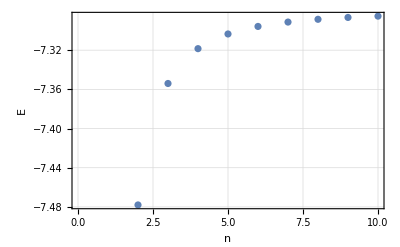

```mathematica
(*From the NIST tables,plot the Li energies vs n and deduce the value of the quantum defect.*)
(*n=2,3,4,… is the principal quantum number of the outer electron.*)

data1=Table[{nlevels⟦j⟧,expt16⟦j⟧},{j,1,9}];
lp1=ThadPlot[ListPlot[data1,PlotRange->{{0,10},All}],{"n","E"}]
```

```mathematica
(* define an effective quantum numbern^*=[2(Subscript[E, ∞]-Subscript[E, n])]^(-1/2) *)

Einf=(-(5.55944459+9.000229392))/2 (*hartree*)

nstar=(2(Einf-expt16))^(-1/2)
```

-7.27984

{1.58854,2.59619,3.59837,4.59932,5.59984,6.60001,7.59984,8.59971,9.60751}

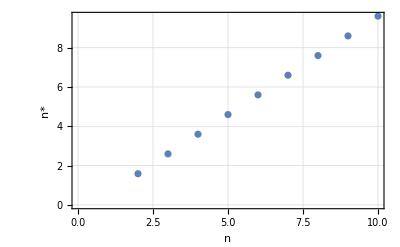

```mathematica
(* plot n^* vs n *)

data2=Table[{nlevels⟦j⟧,nstar⟦j⟧},{j,1,9}];
lp2=ThadPlot[ListPlot[data2,PlotRange->{{0,10},All}],{"n","n*"}]
```

```mathematica
(* Use a Mathematica fitting function such as NonLinearModel-Fit to find δ *)

model[x_,{b_}]:=x+b;
Guessguess={-0.4};
With[{aa={b}},nlm=NonlinearModelFit[data2,model[x,aa],{aa,Guessguess}ᵀ,x]]
```

FittedModel[-0.401186+x]

## what is the meaning of the slope parameter? Can’t just arbitrarily fit for it -1

```mathematica
a={b}/.nlm["BestFitParameters"]
```

{-0.401186}

NIST Quantum Defect Number: 0.401186

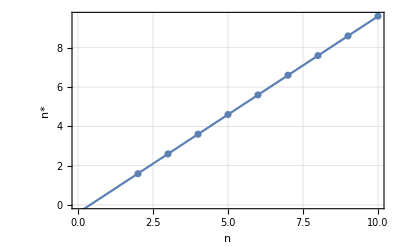

```mathematica
Show[lp2,Plot[model[x,a],{x,0,10}]]
```

## Question 17:

17) Now repeat, but with your calculated energy levels.  Fit to find E_∞ and from that deduce your ionization potential and quantum defect and compare to experiment. 

Also, you should compare your IP you get from the quantum defect analysis to the one you get from just comparing the results of #4 and #14

```mathematica
Ediffnand2 = eval14Dict - eval14Dict⟦1⟧
```

{0.,0.121161,0.156548,0.17186,0.18212,0.186784,0.189686,0.19163,0.193027,0.194522,0.197202,0.202503,0.215121,0.254793,0.604483,2.11024,2.26039,2.28045,2.31578,2.32176,2.33553,2.33927,2.36032,2.36224,2.3751,2.43708,2.45682,2.4803,2.52418,2.64748,2.65275,2.71481,2.76691,2.80895}

```mathematica
FittingModel[nn_,{IP_,δδ_}]:=IP-1/(2(nn-δδ)^2)
GuessGuess17 = {.2, .6};
```

{{2,0.},{3,0.121161},{4,0.156548},{5,0.17186},{6,0.18212},{7,0.186784},{8,0.189686},{9,0.19163},{10,0.193027}}

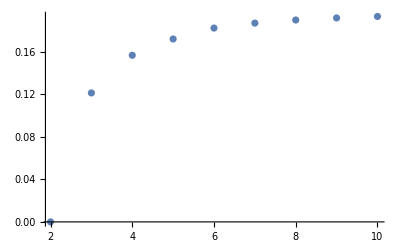

```mathematica
(* PLot n vs E like in #16 *)
data171=Table[{nlevels⟦j⟧,Ediffnand2⟦j⟧},{j,1,9}]
(*lp17=ThadPlot[ListPlot[data17,PlotRange->{{0,9},All}],{"x","y"}]*)
lp171=ListPlot[data171]
```

{{2,0.},{3,0.121161},{4,0.156548},{5,0.17186},{6,0.18212},{7,0.186784},{8,0.189686}}

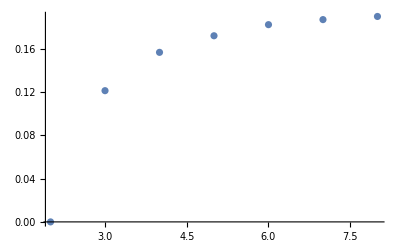

```mathematica
(* PLot n vs E like in #16 *)
(* See discussion below about picking first 7 or so .... *)

data17=Table[{nlevels⟦j⟧,Ediffnand2⟦j⟧},{j,1,7}]
(*lp17=ThadPlot[ListPlot[data17,PlotRange->{{0,9},All}],{"x","y"}]*)
lp17=ListPlot[data17]
```

```mathematica
With[{aa={IP,δδ}},nlm=NonlinearModelFit[data17,FittingModel[x,aa],{aa,GuessGuess17}ᵀ,x]]
```

FittedModel[0.196953-1/(2 (-0.408504+x)^2)]

```mathematica
a17={IP,δδ}/.nlm["BestFitParameters"]
```

{0.196953,0.408504}

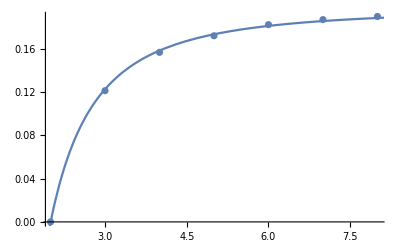

```mathematica
(* PLot n vs E like in #16 *)
Show[lp17,Plot[FittingModel[x,a17],{x,0,10}]]
```

Ionization potential: 0.196953 Hartrees
Quantum Defect Number: 0.408504

We notice that in question 14 when we add more basis states we get a lower percentage on the ground state energy of Li as compared to experiment, but that we get a larger percent difference in the energies in number 15. This exposes a weakness of our model for the higher energy states, so we are only going to fit the lowest 7 since we believe the lower states with more certainty.

```mathematica
(*IP16 = 1.0015012375143624;*)
δδ16=0.40118587413305007;

IP17 = 0.19695307045204274;
δδ17 = 0.40850380091313837;

Percent17Defect = Abs[(1-Abs[δδ17]/Abs[δδ16])]*100
```

1.82407

Our Quantum Defect is 1.82407% different than the one fitted from the NIST data in #16

Use this equation for the calculations below: IP = E_∞ - E_2

```mathematica
IPNISTexp = Einf - (-Nist12);

Percent17IP = (1-IP17/IPNISTexp)*100
```

0.599975

Our Ionization Potential is 0.599975% different than the one expected from NIST data

IP = E_∞ - E_2:

 Ground state energy of Li+ : -7.22701 Hartrees = E infinity 
New ground state energy of the Li atom with minimization process: -7.4191 hartrees = E2

```mathematica
(* From Questions 4 and 14 we can define: and find the ionization potential and compare to the one that we found in the fit for 17: *)

GNDLiPlus = -7.227012460584872;
GNDLi = -7.419200305448957;

IP4and14 = GNDLiPlus - GNDLi
```

0.192188

```mathematica
Percent17IP4and14 = (1-IP4and14/IP17)*100
```

2.41947

The Ionization potential as found from using the results of 4 and 14 is 2.41947% different than the ionization potential found in the fit in #17.

## you should reanalyze your results with the correct NIST δ value